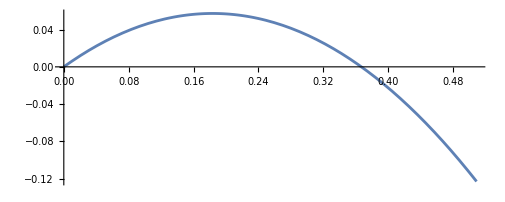

```mathematica
g=9.8;v0=2;θ0=32;
x=v0*Cos[θ0*π/180]*t;
y=v0*Sin[θ0*π/180]*t-1/2*g*t^2;
ParametricPlot[{x,y},{t,0,0.3},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,v0,θ0,x,y]
```

```mathematica
data={a,b,c,d}
data[[2]]=data[[2]]+2
data
Clear[data]
```

{a,b,c,d}

2+b

{a,2+b,c,d}

```mathematica
result={2.5,{x->1.25}};
peak=result[[1]];
peakposition=x/.result[[2]];
Print["Position: ",peakposition,"  peak: ",peak]
Clear[result,peak,peakposition]
```

Position: 1.25  peak: 2.5

```mathematica
data={{a,b},{c,d}};
data[[1]] = data[[1]]*2;
data[[1,2]]=data[[1,2]]+2;
data
TableForm[data]
TableForm[Prepend[data,{"frequence","energy"}]]
MatrixForm[data]
Clear[data]
```

{{2 a,2+2 b},{c,d}}

2 a | 2+2 b
c | d

frequence | energy
2 a | 2+2 b
c | d

(2 a | 2+2 b
c | d)

```mathematica
DSolve[{θ''[t]+η*θ'[t]+Ω^2*θ[t]==0,θ[0]==0,θ'[0]==a},θ[t],t]
```

{{θ[t]→-(a (ⅇ^(1/2 t (-η-√(η^2-4 Ω^2)))-ⅇ^(1/2 t (-η+√(η^2-4 Ω^2)))))/(√(η^2-4 Ω^2))}}

```mathematica
FullSimplify[ExpToTrig[-(a (ⅇ^(1/2 t (-η-ω*ⅈ))-ⅇ^(1/2 t (-η+ω*ⅈ))))/(ω*ⅈ)]]
```

(2 a ⅇ^(-(t η)/2) Sin[(t ω)/2])/ω

```mathematica
η=0.2;Ω=3;
NDSolve[{θ''[t]+η*θ'[t]+Ω^2*θ[t]==0,θ[0]==0,θ'[0]==1},θ[t],{t,0,20}]
```

{{θ[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

```mathematica
Clear[η,Ω]
```

{{θ→InterpolatingFunction[{{0., 10.}}, <>]}}

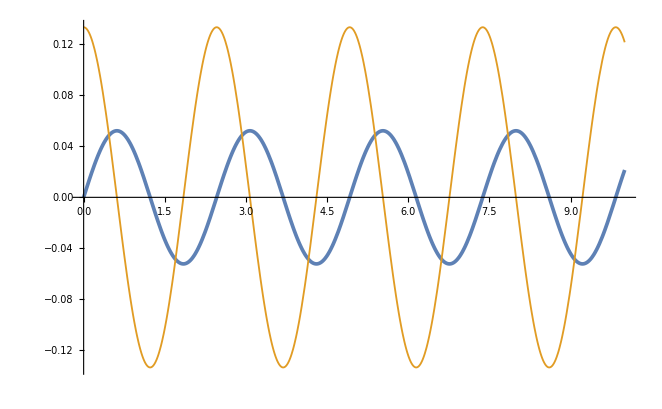

{0.0521699,{t→0.614648}}

{0.0521699,{t→3.07324}}

T=2.45859s

θmax=0.05217 rad, {0.0521699,{t→0.614648}}

```mathematica
g=9.8;L=1.5;Ω=√(g/L);v0=0.2;ω0=v0/L;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,θ'[0]==ω0},θ,{t,0,10}]
θ=θ/.s[[1]];
Plot[{θ[t],θ'[t]},{t,0,10},
PlotStyle->{Thickness[0.004],Thickness[0.002]},
AxesStyle->Thickness[0.003]]
θmax=ArcCos[1-v0^2/(2*g*L)];
θm1=FindMaximum[θ[t],{t,0.5}];
θm2=FindMaximum[θ[t],{t,3}];
T=(t/.θm2[[2]])-(t/.θm1[[2]]);
Print["T=",T,"s"]
Print["θmax=",θmax," rad, ",θm1]
Clear[g,L,Ω,v0,ω0,s,θ,θmax,θm1,θm2,T]
```

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v01=1;
ω01=v01/L;
v02=3;
ω02=v02/L;
as=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,θ'[0]==ω01},θ,{t,0,20}];
θ1=θ/.as[[1]];
bs=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,θ'[0]==ω02},θ,{t,0,20}];
θ2=θ/.bs[[1]];
Animate[
a=ListPlot[{{θ1[t],0}},PlotRange->π/4,
PlotStyle->{Orange,PointSize[0.03]}];
b=ListPlot[{{θ2[t],0}},PlotRange->π/4,
PlotStyle->{Black,PointSize[0.03]}];
Show[{a,b},PlotRange->{{-1,1},{-1,1}}],{t,0,20},ControlPlacement->Top]
Clear[a,b,g,L,Ω,v01,v02,ω01,ω02]
```